```mathematica
SetDirectory[NotebookDirectory[]];
Get[FileNameJoin[{Directory[],"HexaBoxModules.m"}]];
PureIntegrals=ReadList[FileNameJoin[{NotebookDirectory[],"files/PureIntegralBasisFull.txt"}]];
$P=2^31-1;




RemainingInts=PureIntegrals[[103;;]];
```

```mathematica
Position[(RemainingInts/.hxb:>List)[[All,4]],0]
```

{{53},{54},{55},{56},{57},{58},{59},{60},{61}}

```mathematica
RemainingInts[[53;;61]]
```

{hxb[1,0,1,0,0,0,1,1,1,0,0,0,0],hxb[1,0,1,0,0,1,0,1,0,0,0,0,0],hxb[1,0,1,0,0,1,0,1,1,0,0,0,0],hxb[1,0,1,0,0,1,1,1,1,0,0,0,0],hxb[1,0,1,0,1,0,1,1,0,0,0,0,0],hxb[1,0,1,0,1,0,1,1,1,0,0,0,0],hxb[1,0,1,0,1,1,0,1,1,0,0,0,0],hxb[1,0,1,0,1,1,1,1,0,0,0,0,0],hxb[1,0,1,0,1,1,1,1,1,0,0,0,0]}

```mathematica
For[i=53,i<=61,i++,
FactorPlot[i]=plotDiagram[RemainingInts[[i]]];
]
```

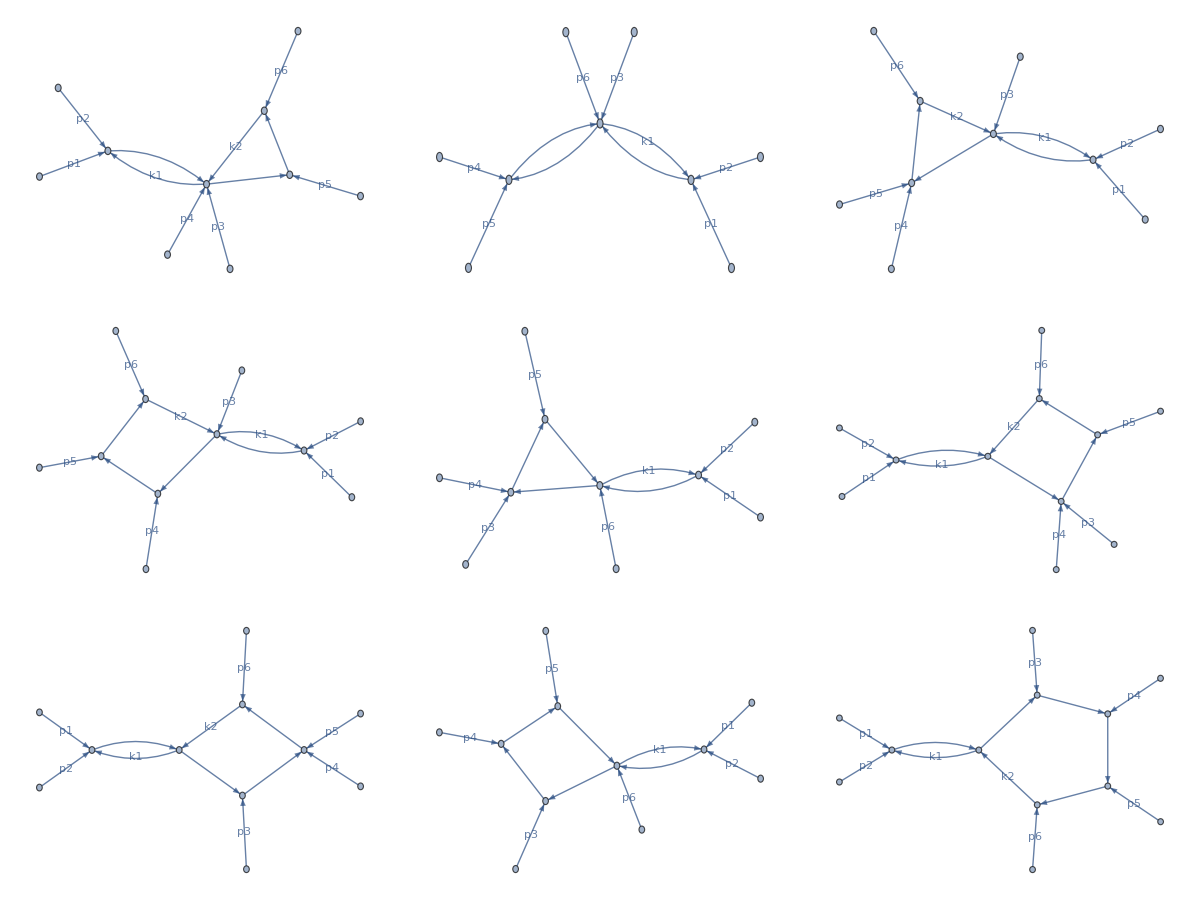

```mathematica
Print[Grid[ArrayReshape[{Table[FactorPlot[i],{i,53,61}]},{3,3}]]];
```

# 1

```mathematica
q[1]=p[1]+p[2]+p[3]+p[4];
q[2]=p[5];
q[3]=-q[1]-q[2];
intMasses={msq[1]->0,msq[2]->0,msq[3]->mt2};
CayleyEntry[i_,j_]:=Module[{mat},
If[i==0 && j==0 ,
Return[0];
];
If[i==0 || j==0 ,
Return[1];
];

If[i==j,
mat=2msq[i]/.intMasses;
Return[mat];
];
If[i<j,
mat=((msq[i]/.intMasses)+(msq[j]/.intMasses)-Expand[(Sum[q[n],{n,i,j-1}])^2])/.mandelstamScalarProducts/.kinematics;
Return[mat];
];
If[i>j,
mat=CayleyEntry[j,i];
Return[mat];
];
]
cutCayley[mat_,l_]:=Module[{res},
res=mat;
res=Delete[res,l];
res=Transpose[Delete[Transpose[res],l]];
res
]
```

```mathematica
modcayleyMat=Table[CayleyEntry[i,j],{i,0,3},{j,0,3}];
modcayleyMat//MatrixForm
k=3+1;
LS=2^(-k/2+1)/root[(-1)^Floor[k/2] Det[modcayleyMat]]
ϵ^3/LS*2(-3+d)
```

(0 | 1 | 1 | 1
1 | 0 | -s56 | 0
1 | -s56 | 0 | 0
1 | 0 | 0 | 2 mt2)

1/(2 root[-4 mt2 s56+s56^2])

4 (-3+d) ϵ^3 root[-4 mt2 s56+s56^2]